```mathematica
ϵ=625000/(22468879468420441π)
ē=-1.602177×10^-19
c=299792458
particlenumber=10^3
duration=10^-8
timestep=10^-10
rmax=1.5*10^-2
delay=rmax/c*0.1
γ[v_]=1/(√(1-v^2/c^2))
γ.b2[v_]=1/(1-v^2/c^2)
electricalForce=-1/(4πϵ);
maxcharge=7000
elecScalForce[Q_,q_,r_Vector]=Qq/Norm[r]^2
elecVecForce[Q_,q_,r_Vector]=Qq/Norm[r]^3*r
elecVecFieldFunc[q_,r_Vector,t_]=Function[
affectedRadius=rmax-c*t;fullyaffected=affectedRadius+delay*c;
distance=Norm[r];(r*q)/distance^3*If[distance≥Min[{Abs[fullyaffected],Abs[affectedRadius]}],If[distance≥Max[{Abs[fullyaffected],Abs[affectedRadius]}],maxcharge,maxcharge 1/2(1+Cos[1/delayc π(Abs[If[affectedRadius<0&&distance<Abs[affectedRadius],distance+affectedRadius,fullyaffected-distance]])])],If[affectedRadius<distance<fullyaffected,maxcharge*1/2(Cos[(distance+affectedRadius)/delayc π]+Cos[(fullyaffected-distance)/delayc π]),0]]];
start=Array[{{RandomReal[{-rmax,rmax}],RandomReal[{-rmax,rmax}]},{RandomReal[40000],RandomReal[40000]}}&,particlenumber];
save={Select[start,Norm[#[[1]]]≤rmax&]};
acctualParticleNumber=Length[save[[1]]];
Do[
copy=save[[-1]];
Do[
thistime=copy[[i]];
particle=thistime[[1]];
particleVel=thistime[[2]];
elecforcevec={0,0};
maxdist=Norm[particle]+rmax;
flashback=1;
eParVel=particleVel/Norm[particleVel];
tmpPos=(particle+(particleVel timestep)/2);
ownγ=γ.b2[particleVel];
While[flashback*c*timestep<maxdist,
scope=If[flashback<2,flashback+1,flashback];
scope=If[scope>Length[save],Length[save],scope];
basis=save[[-scope]];
selection=Select[basis,((flashback-1)timestep*c)^2≤SquaredEuclideanDistance[particle,#1]≤(flashback*timestep*c)^2&];
Do[
test=selection[[n]];
vel=test[[2]];
pos=test[[1]];
eVel=vel/Norm[vel];
VecOfParField+=√(((tmpPos-pos)*eVel)^2+(Norm[(tmpPos-pos)]-(tmpPos-pos)*eVel)^2*γ.b2[vel])*√(((tmpPos-pos)*eParVel)^2+(Norm[(tmpPos-pos)]-(tmpPos-pos)*eParVel)^2*ownγ)*(tmpPos-pos)/Norm[tmpPos-pos]^3
,{n,Length[selection]}];
flashback++
];
charge=(acctualParticleNumber-1)*ē;
vecOfField=vecOfParField*ē*charge*(tmpPos-pos)/Norm[tmpPos-pos]^3+elecVecFieldFunc[ē,particle,timestep*t];














acceleration=elecforcevec*Sqrt[1-Abs[velocity]^2/c^2]/mass;
velocity+=acceleration*timestep;
copy[[i]]={tmppos+velocity*timestep/2,velocity};
,{i,Length[copy]}];
save=Append[copy,save];
,{t,1(*duration/timestep*)}];
```

625000/(22468879468420441 π)

-1.60218×10^-19

299792458

1000

1/100000000

1/10000000000

0.015

5.00346×10^-12

7000

Qq/r^2

1

1

```mathematica
Print[]
```

```mathematica
Qq/r^2
```

Hi

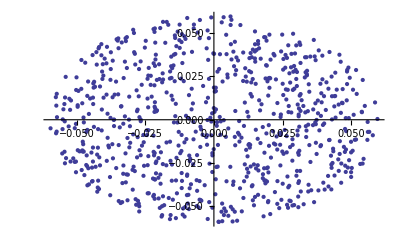

1

```mathematica
ListPlot[#[[1]]&/@save[[1]]]
Length[save]
```

```mathematica
save
```

{{{{-0.0118329,0.018099},{5130.29,12140.6}},«7733»,{{0.00729929,0.0139855},{6278.83,23142.2}}}}

```mathematica
Show[%1134,ImageSize->Medium]
```

-Graphics-

```mathematica
Rasterize[%1135,"Image"]
```

-Graphics-

```mathematica
save
```

{{{0.0260424,0.000164224},{7654.38,36097.3}},«7810»,{{0.0229086,0.00493274},{3263.65,21008.7}}}

```mathematica
Plot[fieldFunction[{0,0.1},n],{n}]
```

Plot::pllim: Range specification {n} is not of the form {x, xmin, xmax}.

```mathematica
par=working
```

{{}[1],{}[2],{}[3],{}[4],{}[5],{}[6],{}[7],{}[8],{}[9],{}[10],{}[11],{}[12],{}[13],{}[14],{}[15],{}[16],«9969»,{}[9986],{}[9987],{}[9988],{}[9989],{}[9990],{}[9991],{}[9992],{}[9993],{}[9994],{}[9995],{}[9996],{}[9997],{}[9998],{}[9999],{}[10000]}

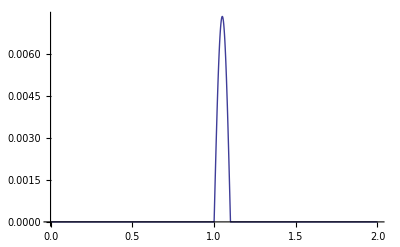

```mathematica
Plot[fieldFunction[{0,0.000000001},n],{n,0*10^-10,2*10^-10}]
```